## Initialisation

```mathematica
(*Velocity distribution*)
ve = 220.0;
σv = 156.0;
vesc = 533.0;

(*Normalisation constant for the velocity distribution*)
Nesc = Erf[vesc/(Sqrt[2]*σv)] - Sqrt[2.0/π]*(vesc/σv)*Exp[-vesc^2/(2σv^2)];
N1 = 1.0/(σv^3 Sqrt[2π]);
N1 = N1/Nesc;
```

```mathematica
PrintTemporary["   Loading PhiIntegrals.dat..."];
```

Tabulate or import the integral of f(v’, θ’, ϕ’) over ϕ’, depending on whether it exists...

```mathematica
filen = NotebookDirectory[] <> "/PhiIntegrals.dat";
If[FileExistsQ[filen],
integralTab= Import[filen];,
integralTab = Flatten[Table[{co, ϕmax,NIntegrate[Exp[co Cos[ϕ]], {ϕ, 0, ϕmax}]},{co, -7,7,0.05},{ϕmax, 0, π+0.1, 0.05}],1];
Export[filen, integralTab, "Table"];];
IntFunϕ = Interpolation[integralTab,InterpolationOrder->1];
```

## Calculating free distributions

#### Integral over ϕ

```mathematica
ClearAll[Integraloverϕ]
Integraloverϕ[x_, ϕmax_]:=
(
Piecewise[{{0, ϕmax  <= 0},{2π BesselI[0, x], ϕmax >= π}}, 2IntFunϕ[x, ϕmax]]
)
```

#### SHM velocity distribution

```mathematica
VelDistFree[v_,θ_,ϕ_, γ_]:=
(
cδ = Sin[γ]*Sin[θ]*Cos[ϕ] + Cos[γ]Cos[θ];
Δsq = v^2 - 2v ve cδ + ve^2; 
Piecewise[{{0, Δsq > vesc^2}, {(N1/(2π ))*Exp[-(Δsq)/(2σv ^2)], Δsq <= vesc^2}}]
)
```

#### SHM velocity distribution (integrated over ϕ)

```mathematica
VelDistInt[v_?NumericQ,θ_?NumericQ, γ_?NumericQ]:=
(
(*In principle, don't need to worry about dividing by zero. I should still work in the case that cosmin -> ∞*)
Δsq = v^2 - 2v ve Cos[γ]Cos[θ] + ve^2;

If[Sin[γ]Sin[θ] == 0, 2 π VelDistFree[v, θ, 0, γ],

cosmin = (v^2+ve^2-vesc^2)/(2 v ve Sin[γ]Sin[θ])-(Cos[γ]Cos[θ])/(Sin[γ]Sin[θ]);
(*fudge = ArcCos[Max[tester,-1]]/(π);*)
Integraloverϕ[Sin[θ]Sin[γ] v ve /(σv^2),Re[ArcCos[Min[Max[cosmin,-1.0],1.0]]]](N1/(2π ))*Exp[-(Δsq)/(2σv ^2)]]
)
```

#### SHM speed distribution

```mathematica
SpeedDistFree[v_?NumericQ]:=
(
Piecewise[{{0,v >= vesc + ve }, 
{ β = v*ve/σv^2;
(N1/β)*v^2*Exp[-(v^2 + ve^2)/(2.0σv^2)]*(Exp[β] - Exp[(v^2 + ve^2 - vesc^2)/(2.0 σv^2)]), (v < vesc + ve)&&(v > vesc - ve)},
 { β = v*ve/σv^2;(N1/β)*v^2*Exp[-(v^2 + ve^2)/(2.0σv^2)]*(Exp[β] - Exp[-β]) ,v <= vesc - ve}}]
)
```

#### Average DM speed

```mathematica
vavg = NIntegrate[v SpeedDistFree[v], {v, 0, 753}];
```

## Calculations

```mathematica
vbar[t_, v0]:= v0/(1+v0 λ t)
```

```mathematica
Assuming[Re[1/(t v0 λ)] ≥ 0,Integrate[vbar[τ, v0]^4, {τ, 0, t}]]
```

(t v0^4 (3+t v0 λ (3+t v0 λ)))/(3 (1+t v0 λ)^3)

```mathematica
0.0035*180/π
```

0.200535

Distance travelled underground

```mathematica
l = 1.5
RE = 6371.0
rdet = RE-l
```

1.5

6371.

6369.5

```mathematica
d1[θi_]:=-Cos[θi] rdet +Sqrt[(Cos[θi] rdet)^2 - (rdet^2 - RE^2)]
d2[θi_]:=-Cos[θi] rdet -Sqrt[(Cos[θi] rdet)^2 - (rdet^2 - RE^2)]
```

10^12 -> 10^-22.6

```mathematica
10^-22.6
```

2.51189×10^-23

```mathematica
LUXlim[mx_] := N[10^-43*mx/10^5];
```

```mathematica
A = 16;
mx=10^12;
σ = A^4 1 10^-22;
nA = 10^23;
λ = N[10^-5/(nA σ)]
LUXlim[mx]
```

1.52588×10^-11

1.×10^-36

5/32768

```mathematica
Exp[-d1[0]*(A*0.9315/mx)/λ]
```

0.23105

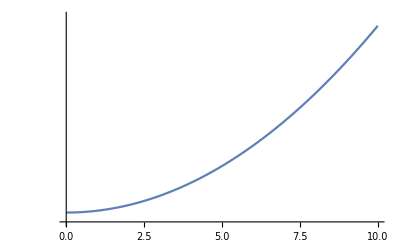

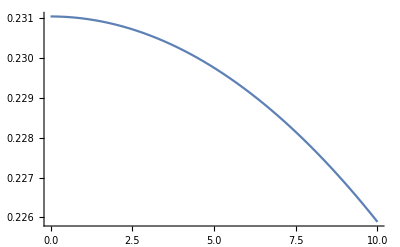

```mathematica
LogPlot[d1[θ*π/180.0], {θ, 0, 10}]
Plot[Exp[-d1[θ*π/180.0]*(A*0.9315/mx)/λ], {θ, 0, 10}]
```

```mathematica
γ = 0;
```

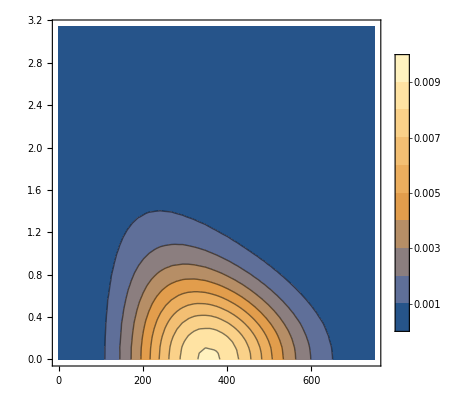

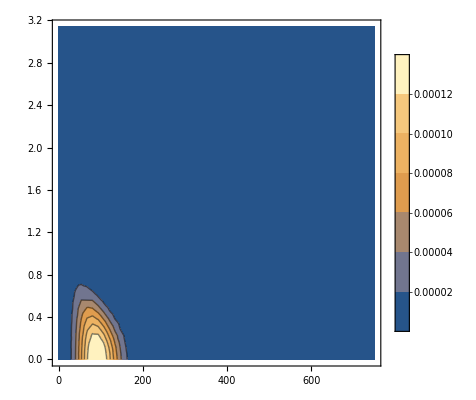

```mathematica
ContourPlot[v^2 VelDistInt[v,θ, γ],{v,0.1, 750}, {θ, 0, π}, PlotLegends->Automatic, PlotRange-> All]
ContourPlot[v^2 VelDistInt[v/Exp[-d1[θ]*(A*0.9315/mx)/λ],θ, γ]Exp[-d1[θ]*(A*0.9315/mx)/λ],{v,0.1, 750}, {θ, 0, π}, PlotLegends->Automatic, PlotRange-> All]
```

```mathematica
NIntegrate[v^2 Sin[θ]VelDistInt[v,θ, π/3],{v,0.1, 750}, {θ, 0, π}, Method->{"QuasiMonteCarlo", MaxPoints->10000}]
```

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.999599 and 0.0162726 for the integral and error estimates.

0.999599

```mathematica
750*Exp[-d1[0]*(A*0.9315/mx)/λ]
```

191.067

```mathematica
ηfree[vmin_]:= NIntegrate[v Sin[θ]VelDistInt[v,θ, 0],{v,vmin, 750}, {θ, 0, π}, Method->{"QuasiMonteCarlo", MaxPoints->10000}]
```

```mathematica
ηpert[vmin_]:= NIntegrate[v Sin[θ]VelDistInt[v/Exp[-d1[θ]*(A*0.9315/mx)/λ],θ, γ],{v,vmin, 750*Exp[-d1[0]*(A*0.9315/mx)/λ]}, {θ, 0, π}, Method->{"QuasiMonteCarlo", MaxPoints->10000}]
```

```mathematica
vlist = Table[v, {v, 0, 750, 25}]
```

{0,25,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400,425,450,475,500,525,550,575,600,625,650,675,700,725,750}

```mathematica
ηtab = Table[{v,ηfree[v]}, {v, vlist}];
```

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.00384145 and 0.0000694449 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0038177 and 0.0000679026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.00374458 and 0.0000665553 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
ηtabpert =  Table[{v,ηpert[v]}, {v, vlist}]
```

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0000919525 and 2.90377×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0000822406 and 2.64472×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 6828 integrand evaluations. NIntegrate obtained 0.0000571637 and 2.05214×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{{0,0.0000919525},{25,0.0000822406},{50,0.0000571637},{75,0.0000298534},{100,0.0000113821},{125,3.06927×10^-6},{150,5.41952×10^-7},{175,3.92547×10^-8},{200,-5.21996×10^-11},{225,-4.94101×10^-11},{250,-8.45723×10^-11},{275,-4.41175×10^-11},{300,-5.68095×10^-11},{325,-6.92995×10^-11},{350,-8.15896×10^-11},{375,0.},{400,0.},{425,0.},{450,0.},{475,0.},{500,0.},{525,0.},{550,0.},{575,0.},{600,0.},{625,0.},{650,0.},{675,0.},{700,0.},{725,0.},{750,0.}}

```mathematica
ηrat = Transpose[{vlist, ηtabpert[[All, 2]]/ηtab[[All, 2]]}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{{0,0.0239369},{25,0.0215419},{50,0.0152657},{75,0.00823415},{100,0.0032864},{125,0.000940642},{150,0.00017891},{175,0.000014171},{200,-2.09356×10^-8},{225,-2.23853×10^-8},{250,-4.40397×10^-8},{275,-2.68909×10^-8},{300,-4.1301×10^-8},{325,-6.1274×10^-8},{350,-8.95159×10^-8},{375,0.},{400,0.},{425,0.},{450,0.},{475,0.},{500,0.},{525,0.},{550,0.},{575,0.},{600,0.},{625,0.},{650,0.},{675,0.},{700,0.},{725,0.},{750,Indeterminate}}

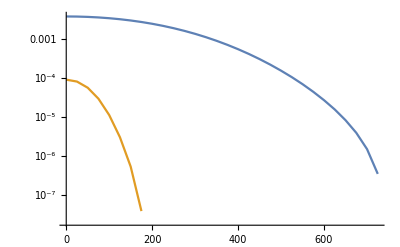

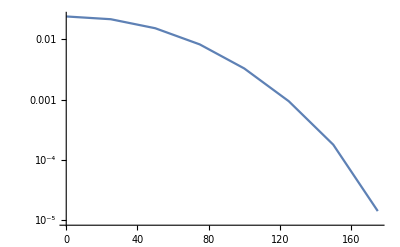

```mathematica
ListLogPlot[{ηtab, ηtabpert}, Joined->True]
ListLogPlot[ηrat, Joined->True]
```

```mathematica
f[Eχ_]:= Exp[- β Eχ] + γ Eχ Exp[-δ Eχ]
```

```mathematica
Integrate[1/(Eχ f[Eχ]), Eχ]
```

∫1/(Eχ (ⅇ^(-Eχ β)+ⅇ^(-Eχ δ) Eχ γ))ⅆEχ

```mathematica
f2[x_]:=Integrate[1/(Eχ Exp[- α Eχ]), {Eχ, E0, x}]
```

```mathematica
E0 = 750^2
α = 1.0
```

562500

1.

```mathematica
Integrate[1/(Eχ Exp[- α Eχ]),Eχ]
```

ExpIntegralEi[1. Eχ]

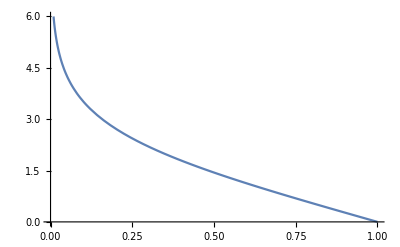

```mathematica
Plot[ExpIntegralEi[1]-ExpIntegralEi[Eχ],{Eχ, 0, 1}]
```